## 1.

### a)

```mathematica
Normal[Series[u[y],{y,x , 2}]]
```

u[x]+(-x+y) u'[x]+1/2 (-x+y)^2 u''[x]

```mathematica
Un2 = u[x+k]+k u'[x+k]+1/2 (k)^2 u''[x+k]
Un = u[x+k]-k u'[x+k]+1/2 (-k)^2 u''[x+k]
(1/2 u[x+k] + 1/2 Un -Un2)/(2k)+u'[x+k] //FullSimplify
```

u[k+x]+k u'[k+x]+1/2 k^2 u''[k+x]

u[k+x]-k u'[k+x]+1/2 k^2 u''[k+x]

1/8 (2 u'[k+x]-k u''[k+x])

## 2.

```mathematica
Factor[2 z^3-5 z^2+4z-1]
```

(-1+z)^2 (-1+2 z)

```mathematica
3 - 20 + 8/2^10
```

-2175/128

```mathematica
N[-2175/128]
```

-16.9922

```mathematica
NumberForm[-16.9921875,16]
```

-16.9921875

```mathematica
Manipulate[RegionPlot[Abs[(-1-(x + ⅈ y)+(x + ⅈ y)θ)/(1 - (x + ⅈ y)θ)]≤1,{x,-5,5},{y,-5,5},Axes->True,Frame->False,AxesLabel->{"Real","Imaginary"},PlotLabel->"θ = "<>ToString[θ]],{θ,0,1}]
```

```mathematica
(-1-z+z θ)/(1 - z θ)//FullSimplify
```

-1+z/(-1+z θ)

```mathematica
Simplify[Abs[(-1-x-ⅈ y+(x+ⅈ y) θ)/(1-(x+ⅈ y) θ)]]
```

Abs[(1+x-ⅈ y (-1+θ)-x θ)/(-1+x θ+ⅈ y θ)]

```mathematica
Sqrt[((-1-(x + ⅈ y)+(x + ⅈ y)θ)/(1 - (x + ⅈ y)θ))((-1-(x - ⅈ y)+(x - ⅈ y)θ)/(1 - (x - ⅈ y)θ))]//FullSimplify
```

√(1+(x (2+x)+y^2-2 (x^2+y^2) θ)/(1-2 x θ+(x^2+y^2) θ^2))

```mathematica
(-1-z+z θ)/(1 - z θ)
((-1-z+z θ)(-1-SuperStar[z]+SuperStar[z] θ))/((1 - z θ)(1-SuperStar[z] θ))
((-1-z+z θ)(-1-SuperStar[z]+SuperStar[z] θ))/((1 - z θ)(1-SuperStar[z] θ))
```

(-1-z+z θ)/(1-z θ)

1/((1-z θ) (1-θ z^*))+z/((1-z θ) (1-θ z^*))-(z θ)/((1-z θ) (1-θ z^*))+z^*/((1-z θ) (1-θ z^*))+(z z^*)/((1-z θ) (1-θ z^*))-(θ z^*)/((1-z θ) (1-θ z^*))-(2 z θ z^*)/((1-z θ) (1-θ z^*))+(z θ^2 z^*)/((1-z θ) (1-θ z^*))

## 4.

```mathematica
γ = √3/6;
Solve[{Y1 ==λ(Un + 1/4 k Y1 + (1/4-γ)k Y2),Y2 == λ(Un + (1/4+γ)k Y1+1/4 k Y2)},{Y1,Y2}]
```

{{Y1→-(2 (-6 Un λ+√3 k Un λ^2))/(12-6 k λ+k^2 λ^2),Y2→(2 λ (6 Un+√3 k Un λ))/(12-6 k λ+k^2 λ^2)}}

```mathematica
Un1 = Un + 1/2 k(-(2 (-6 Un λ+√3 k Un λ^2))/(12-6 k λ+k^2 λ^2)+(2 λ (6 Un+√3 k Un λ))/(12-6 k λ+k^2 λ^2))
```

Un+1/2 k ((2 λ (6 Un+√3 k Un λ))/(12-6 k λ+k^2 λ^2)-(2 (-6 Un λ+√3 k Un λ^2))/(12-6 k λ+k^2 λ^2))

```mathematica
Un1//FullSimplify
```

Un+(12 k Un λ)/(12+k λ (-6+k λ))

```mathematica
(1 + (12 k λ)/(12 + k λ (-6 + k λ)))Un
((12 +6k λ+(k λ)^2)/(12 -6k λ+(k λ)^2))Un == ⅇ^(k λ)Un + O[k^5]
```

```mathematica
Series[(12 +6z+(z)^2)/(12 -6z+(z)^2)-ⅇ^z,{z,0,10}]
```

-z^5/720-z^6/720-(47 z^7)/60480-(19 z^8)/60480-z^9/10080-(59 z^10)/2419200+O[z]^11

```mathematica
R[z_]:=(12 +6z+(z)^2)/(12 -6z+(z)^2)
```

### b)

```mathematica
Abs[R[z]]≤1//FullSimplify
```

Abs[1+(12 (x+ⅈ y))/(12+x^2+2 ⅈ x (3 ⅈ+y)-y (6 ⅈ+y))]≤1

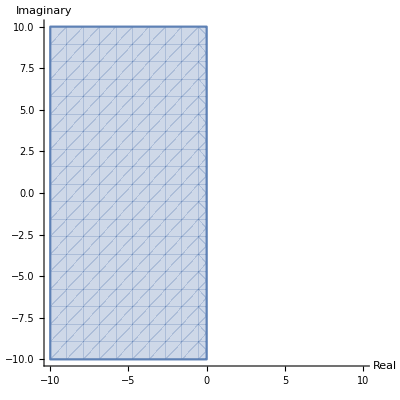

```mathematica
RegionPlot[Abs[R[x + ⅈ y]]≤1,{x,-10,10},{y,-10,10},Axes->True,Frame->False,AxesLabel->{"Real","Imaginary"}]
```

Yes it is A-stable

### c)

No this method is not L-stable because the limit of |R(z)| as z goes to infinity on the positive real axis is 1 not zero.